```mathematica
(*Question One*)
```

```mathematica
f[x_]=x*Exp[-x]-1
```

-1+ⅇ^-x x

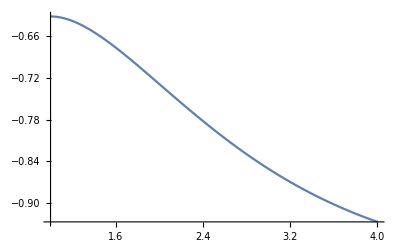

```mathematica
Plot[f[x], {x,1,4}]
```

```mathematica
(*Cubic Taylor Expansion*)
l[x_]=D[f[x],x];
m[x_]=D[f[x],x,x];
o[x_]=D[f[x],x,x,x];
g[x_]=f[2.5]+(l[2.5]*(x-2.5))+(1/(2!)*m[2.5]*(x-2.5)^2)+(1/(3!)*o[2.5]*(x-2.5)^3)
```

-0.794788-0.123127 (-2.5+x)+0.0205212 (-2.5+x)^2+0.00684042 (-2.5+x)^3

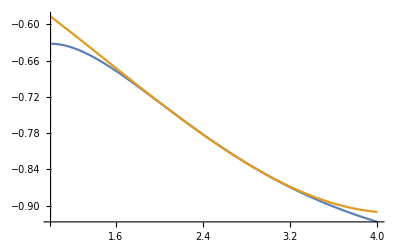

```mathematica
Plot[{f[x],g[x]} ,{x,1,4}]
```

```mathematica
(*Norm Error*)
NE=(∫_1^4 (f[x]-g[x])^2ⅆx)^(1/2)
```

0.0187681

```mathematica
(*Mean Norm Error*)
MNE=1/(4-1)(∫_1^4 (f[x]-g[x])^2ⅆx)^(1/2)
```

0.00625605

```mathematica
(*Question Two*)
```

```mathematica
(*Q2 Part A*)
```

```mathematica
k[x_]=InterpolatingPolynomial[{{1,f[1]},{2,f[2]},{3,f[3]},{4,f[4]}},x]
```

-1+1/ⅇ+(2/ⅇ^2-1/ⅇ+(1/2 (3/ⅇ^3-4/ⅇ^2+1/ⅇ)+1/3 (1/2 (4/ⅇ^4-6/ⅇ^3+2/ⅇ^2)+1/2 (-3/ⅇ^3+4/ⅇ^2-1/ⅇ)) (-3+x)) (-2+x)) (-1+x)

```mathematica
Expand[k[x]]
```

-1-4/ⅇ^4+12/ⅇ^3-12/ⅇ^2+4/ⅇ+(22 x)/(3 ⅇ^4)-(21 x)/ⅇ^3+(19 x)/ⅇ^2-(13 x)/(3 ⅇ)-(4 x^2)/ⅇ^4+(21 x^2)/(2 ⅇ^3)-(8 x^2)/ⅇ^2+(3 x^2)/(2 ⅇ)+(2 x^3)/(3 ⅇ^4)-(3 x^3)/(2 ⅇ^3)+x^3/ⅇ^2-x^3/(6 ⅇ)

```mathematica
(*Q2 Part B*)
```

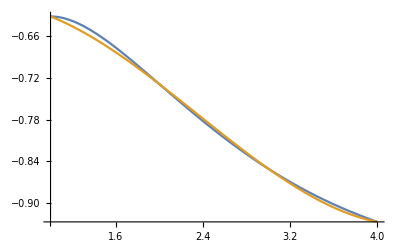

```mathematica
Plot[{f[x],k[x]},{x,1,4}]
```

```mathematica
(*Q2 Part C*)
```

```mathematica
(*Q2 Norm Error*)
NE2=(∫_1^4 (f[x]-k[x])^2ⅆx)^(1/2)
```

(√(1/35 (41637+ⅇ (-64086+ⅇ (35474+ⅇ (-7205+ⅇ (3534+ⅇ (-2141+347 ⅇ))))))))/(2 ⅇ^4)

```mathematica
N[NE2]
```

0.00748051

```mathematica
(*Q2 Mean Norm Error*)
MNE2=1/(4-1)(∫_1^4 (f[x]-k[x])^2ⅆx)^(1/2)
```

(√(1/35 (41637+ⅇ (-64086+ⅇ (35474+ⅇ (-7205+ⅇ (3534+ⅇ (-2141+347 ⅇ))))))))/(6 ⅇ^4)

```mathematica
N[MNE2]
```

0.0024935

```mathematica
(*Q2 Part D*)
```

```mathematica
Grid[{{Text["C.T.I. Norm Error"],Text["C.T.I. Mean Norm Error"], Text["P.I. Norm Error"], Text["P.I. Mean Norm Error"]},{NE, MNE, N[NE2], N[MNE2]}}, Frame->All]
```

C.T.I. Norm Error | C.T.I. Mean Norm Error | P.I. Norm Error | P.I. Mean Norm Error
0.0187681 | 0.00625605 | 0.00748051 | 0.0024935

```mathematica
(*As shown on the graph above the p for Polynomial Interpolation is better than the p of Cubic Taylor Interplant*)
```

```mathematica
(*Q2 Part E*)
```

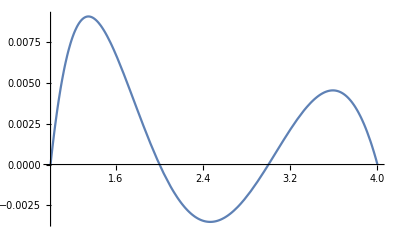

```mathematica
Plot[{f[x]-k[x]},{x,1,4}]
```

```mathematica
f[2.5]-k[2.5]
```

-0.003484

```mathematica
(*Question Three*)
```

```mathematica
h[x_]=1/(1+x^2)
```

1/(1+x^2)

```mathematica
j[x_]=InterpolatingPolynomial[{h[-2],h[-1],h[0],h[1],h[2]},x]
```

1/5+(3/10+(1/10+(-1/5+1/10 (-4+x)) (-3+x)) (-2+x)) (-1+x)

```mathematica
Expand[j[x]]
```

37/10-(36 x)/5+(24 x^2)/5-(6 x^3)/5+x^4/10

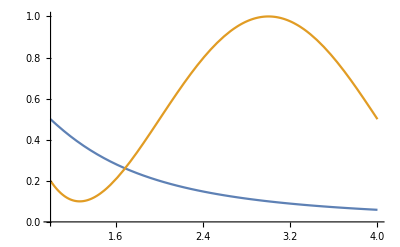

```mathematica
Plot[{h[x],j[x]},{x,1,4}]
```

```mathematica
(*Q3 Norm Error*)
```

```mathematica
NE3=(∫_1^4 (h[x]-j[x])^2ⅆx)^(1/2)
```

√(-194532/14875-(5 π)/8+(5 ArcTan[4])/2-6 Log[2]+6 Log[17])

```mathematica
N[NE3]
```

1.0553

```mathematica
(*Q3 Mean Norm Error*)
```

```mathematica
MNE3=1/(4-1)(∫_1^4 (h[x]-j[x])^2ⅆx)^(1/2)
```

1/3 √(-194532/14875-(5 π)/8+(5 ArcTan[4])/2-6 Log[2]+6 Log[17])

```mathematica
N[MNE3]
```

0.351768

```mathematica
(*Bonus Work*)
t[x_]=2x^4+100;
```

100+2 x^4

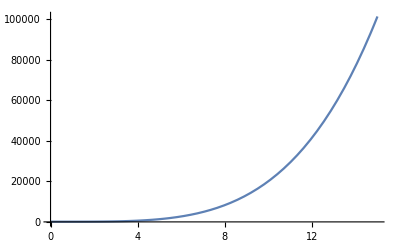

```mathematica
Plot[t[x],{x,0,15}]
```

```mathematica
(*Cubic Taylor Expansion*)
dt[x_]=D[t[x],x];
ddt[x_]=D[t[x],x,x];
dddt[x_]=D[t[x],x,x,x];
u[x_]=t[2.5]+(dt[2.5]*(x-2.5))+(1/(2!)*ddt[2.5]*(x-2.5)^2)+(1/(3!)*dddt[2.5]*(x-2.5)^3)
```

178.125+125. (-2.5+x)+75. (-2.5+x)^2+20. (-2.5+x)^3

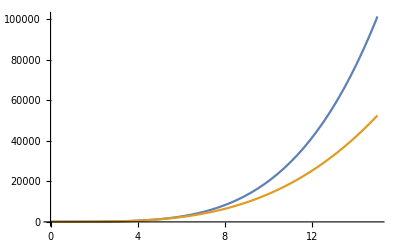

```mathematica
Plot[{t[x],u[x]},{x,0,15}]
```

```mathematica
v[x_]=InterpolatingPolynomial[{t[0],t[1],t[2],t[3],t[4],t[5],t[6],t[7],t[8],t[9]},x]
```

100+(2+(14+(12+2 (-4+x)) (-3+x)) (-2+x)) (-1+x)

```mathematica
Expand[v[x]]
```

102-8 x+12 x^2-8 x^3+2 x^4

```mathematica
dv[x_]=D[v[x],x];
ddv[x_]=D[v[x],x,x];
dddv[x_]=D[v[x],x,x,x];
```

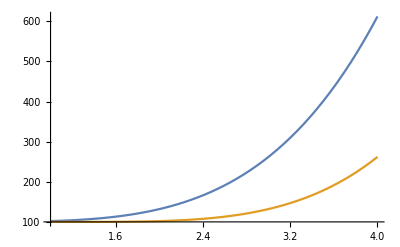

```mathematica
Plot[{t[x],v[x]},{x,1,4}]
```

```mathematica
NE4=(∫_1^4 (t[x]-v[x])^2ⅆx)^(1/2);
```

2 √(544623/35)

```mathematica
MNE4=1/(4-1)(∫_1^4 (t[x]-v[x])^2ⅆx)^(1/2);
```

2 √(181541/105)

```mathematica
NE5=(∫_1^4 (dt[x]-dv[x])^2ⅆx)^(1/2);
```

4 √(19338/5)

```mathematica
MNE5=1/(4-1)(∫_1^4 (dt[x]-dv[x])^2ⅆx)^(1/2);
```

4 √(6446/15)

```mathematica
NE6=(∫_1^4 (ddt[x]-ddv[x])^2ⅆx)^(1/2);
```

24 √57

```mathematica
MNE6=1/(4-1)(∫_1^4 (ddt[x]-ddv[x])^2ⅆx)^(1/2);
```

8 √57

```mathematica
NE7=(∫_1^4 (dddt[x]-dddv[x])^2ⅆx)^(1/2);
```

48 √3

```mathematica
MNE7=1/(4-1)(∫_1^4 (dddt[x]-dddv[x])^2ⅆx)^(1/2);
```

16 √3

1st Der Norm Error | 1st Der Mean Norm Error | 2nd Der Norm Error | 2nd Der Mean Norm Error | 3rd Der Norm Error | 3rd Der Mean Norm Error
248.76 | 82.92 | 181.196 | 60.3987 | 83.1384 | 27.7128

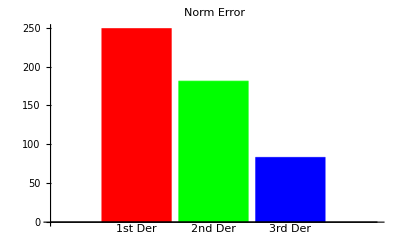

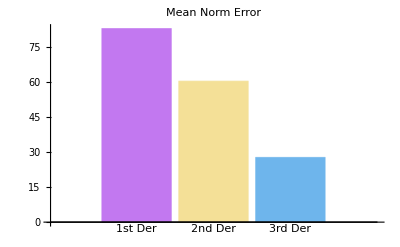

```mathematica
Grid[{{Text["1st Der Norm Error"],Text["1st Der Mean Norm Error"], Text["2nd Der Norm Error"], Text["2nd Der Mean Norm Error"],Text["3rd Der Norm Error"], Text["3rd Der Mean Norm Error"]},{N[NE5], N[MNE5],N[NE6], N[MNE6], N[NE7], N[MNE7]}}, Alignment->{Center,Automatic},Frame->All]
data1=List[{N[NE5],N[NE6],N[NE7]}];
data2=List[{N[MNE5],N[MNE6],N[MNE7]}];
BarChart[data1, ChartLabels->{"1st Der","2nd Der","3rd Der"},PlotLabel->"Norm Error",ChartStyle->{Red, Green, Blue, Yellow}]
BarChart[data2, ChartLabels->{"1st Der","2nd Der","3rd Der"},PlotLabel->"Mean Norm Error",ChartStyle->"Pastel"]
```

```mathematica
Text["Rate of Duck Growth With No Predators"]
t[x_]=2x^4+100
Plot[t[x],{x,0,15},PlotLabel->"Growth Rate",PlotLegends->{"t[x]"}]
dt[x_]=D[t[x],x];
ddt[x_]=D[t[x],x,x];
dddt[x_]=D[t[x],x,x,x];
Text["Cubic Taylor Expansion of Duck Growth"]
u[x_]=t[2.5]+(dt[2.5]*(x-2.5))+(1/(2!)*ddt[2.5]*(x-2.5)^2)+(1/(3!)*dddt[2.5]*(x-2.5)^3);
Expand[u[x]]
Plot[{t[x],u[x]},{x,0,15},PlotLabel->"Growth Rate vs. C.T.E",PlotLegends->{"t[x]","u[x]"}]
Text["Polynomial Interpolation"]
v[x_]=InterpolatingPolynomial[{t[0],t[1],t[2],t[3],t[4],t[5],t[6],t[7],t[8],t[9]},x];
Expand[v[x]]
dv[x_]=D[v[x],x];
ddv[x_]=D[v[x],x,x];
dddv[x_]=D[v[x],x,x,x];
Plot[{t[x],v[x]},{x,1,15},PlotLabel->"Growth Rate vs. P.I.",PlotLegends->{"t[x]","v[x]"}]
NE4=(∫_1^4 (t[x]-v[x])^2ⅆx)^(1/2);
MNE4=1/(4-1)(∫_1^4 (t[x]-v[x])^2ⅆx)^(1/2);
NE5=(∫_1^4 (dt[x]-dv[x])^2ⅆx)^(1/2);
MNE5=1/(4-1)(∫_1^4 (dt[x]-dv[x])^2ⅆx)^(1/2);
NE6=(∫_1^4 (ddt[x]-ddv[x])^2ⅆx)^(1/2);
MNE6=1/(4-1)(∫_1^4 (ddt[x]-ddv[x])^2ⅆx)^(1/2);
NE7=(∫_1^4 (dddt[x]-dddv[x])^2ⅆx)^(1/2);
MNE7=1/(4-1)(∫_1^4 (dddt[x]-dddv[x])^2ⅆx)^(1/2);
Plot[{t[x],u[x],v[x]},{x,1,15},PlotLabel->"Growth Rate vs. C.T.E. vs. P.I.",PlotLegends->{"t[x]","u[x]","v[x]"}]
data1=List[{N[NE4],N[NE5],N[NE6],N[NE7]}];
data2=List[{N[MNE4],N[MNE5],N[MNE6],N[MNE7]}];
Grid[{{Text["Base Norm Error"],Text["First Der. Norm Error"], Text["Second Der. Norm Error"],Text["Third Der. Norm Error"]},{N[NE4],N[NE5],N[NE6], N[NE7]}}, Alignment->{Center,Automatic},Frame->All]
BarChart[data1, ChartLabels->{"Base","1st Der","2nd Der","3rd Der"},PlotLabel->"Norm Error",ChartStyle->{Red, Green, Blue, Yellow}]
Grid[{{Text["Base Mean Norm Error"],Text["First Der. Mean Norm Error"], Text["Second Der. Mean Norm Error"],Text["Third Der. Mean Norm Error"]},{N[MNE4],N[MNE5],N[MNE6], N[MNE7]}}, Alignment->{Center,Automatic},Frame->All]
BarChart[data2, ChartLabels->{"Base","1st Der","2nd Der","3rd Der"},PlotLabel->"Mean Norm Error",ChartStyle->"Pastel"]
```